## NIG factor model stuff

```mathematica
Clear[α,β,μ,δ,μ1,μ2,δ1,δ2]
```

See https://en.wikipedia.org/wiki/Bessel_function: The modified Bessel function of the second kind has also been called [..] Modified Bessel function of the third kind.

```mathematica
q[x_]:=√(1+x^2);
g[x_,α_,β_,μ_,δ_]:=(α Exp[δ √(α^2-β^2)-β μ] BesselK[1,δ α q[(x-μ)/δ]] Exp[β x])/(π q[(x-μ)/δ]);
```

```mathematica
M[u_,α_,β_,μ_,δ_]:=Exp[δ (√(α^2-β^2)-√(α^2-(β+u)^2))+μ u]
```

Expectation

```mathematica
Simplify[D[M[u,α,β,μ,δ], u]/.u->0]
```

(β δ)/(√(α^2-β^2))+μ

```mathematica
ENIG[α_,β_,μ_,δ_]:=μ+(δ β)/(√(α^2-β^2));
```

Variance

```mathematica
Simplify[D[M[u,α,β,μ,δ], {u,2}]-ENIG[α,β,μ,δ]^2/.u->0]
```

(α^2 δ)/((α^2-β^2)^(3/2))

```mathematica
VNIG[α_,β_,μ_,δ_]:=(α^2 δ)/((α^2-β^2)^(3/2));
```

Skewness
(see https://en.wikipedia.org/wiki/Skewness)

```mathematica
Simplify[(D[M[u,α,β,μ,δ], {u,3}]-3 ENIG[α,β,μ,δ] VNIG[α,β,μ,δ]-ENIG[α,β,μ,δ]^3)/VNIG[α,β,μ,δ]^(3/2)/.u->0,Assumptions->{α>0,α^2-β^2>0}]
```

(3 β)/(α √δ (α^2-β^2)^(1/4))

```mathematica
SNIG[α_,β_,μ_,δ_]:=(3 β)/(α √δ (α^2-β^2)^(1/4))
```

Centering inside the moment generating function:

```mathematica
Simplify[D[M[u,α,β,-(δ β)/(√(α^2-β^2)),δ], {u,3}]/VNIG[α,β,μ,δ]^(3/2)/.u->0,Assumptions->{α>0,α^2-β^2>0,δ>0}]
```

(3 β)/(α √δ (α^2-β^2)^(1/4))

```mathematica
Simplify[D[M[u,α,β,-(δ β)/(√(α^2-β^2)),δ], {u,3}]/VNIG[α,β,μ,δ]^(3/2)/.u->0,Assumptions->{α>0,α^2-β^2>0,δ>0}]
```

(3 β)/(α √δ (α^2-β^2)^(1/4))

Kurtosis

```mathematica
Simplify[D[M[u,α,β,-(δ β)/(√(α^2-β^2)),δ], {u,4}]/VNIG[α,β,μ,δ]^2/.u->0,Assumptions->α>0]
```

(3 (α^2+4 β^2))/(α^2 δ √(α^2-β^2))+3

```mathematica
KNIG[α_,β_,μ_,δ_]:=(3 (α^2+4 β^2))/(α^2 δ √(α^2-β^2))+3
```

Simulate  NIG’s

```mathematica
d[x_,α_,β_,δ_]:=(Exp[δ √(α^2-β^2)] x^(-3/2) Exp[-(δ^2/x+(α^2-β^2) x)/2])/(√(2 π))
```

```mathematica
μ=0;
μ1=-1;
μ2=0.5;
δ=0.5;
δ1=2;
δ2=1;
β=-3;
α=8;
γ=√(α^2-β^2);
μIG=δ/γ;
μ1IG=δ1/γ;
μ2IG=δ2/γ;
λ=δ^2;
λ1=δ1^2;
λ2=δ2^2;
```

```mathematica
n=100000;
Y=RandomVariate[NormalDistribution[],{3,n}];
W = RandomVariate[InverseGaussianDistribution[μIG,λ], n];
W1 = RandomVariate[InverseGaussianDistribution[μ1IG,λ1], n];
W2 = RandomVariate[InverseGaussianDistribution[μ2IG, λ2], n];
```

```mathematica
Z=μ+β W+√W Y⟦3⟧;
Z1=μ1+β W1+√W1 Y⟦1⟧;
Z2=μ2+β W2+√W2 Y⟦2⟧;
```

```mathematica
X1 = Z + Z1;
X2 = Z + Z2;
```

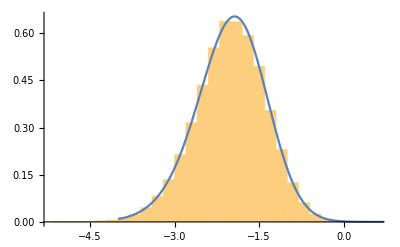
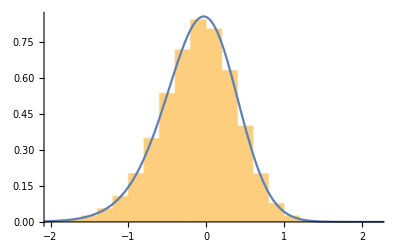

```mathematica
{Show[
Histogram[X1,Automatic, "PDF"],
Plot[g[x,α,β,μ+μ1,δ+δ1], {x,-4,5}]
],
Show[
Histogram[X2,Automatic, "PDF"],
Plot[g[x,α,β,μ+μ2,δ+δ2], {x,-4,5},PlotRange->Full]
]}
```

```mathematica
EX1=ENIG[α, β, μ+μ1,δ+δ1];
EX2=ENIG[α, β,μ+μ2,δ+δ2];
```

```mathematica
VX1=VNIG[α,β,μ+μ1,δ+δ1];
VX2=VNIG[α,β, μ+μ2,δ+δ2];
VZ = VNIG[α,β,μ,δ];
```

```mathematica
N[{{Mean[X1], EX1}, {Variance[X1], VX1}, {Mean[X2],EX2}, {Variance[X2], VX2}}//TableForm]
```

-2.01043 | -2.0113
0.390895 | 0.392262
-0.107339 | -0.10678
0.236465 | 0.235357

Covariance

```mathematica
N[{VZ, Covariance[X1,X2]}]
```

{0.0784523,0.0787964}

Correlation

```mathematica
N[{√(δ^2/((δ+δ1) (δ+δ2))),Correlation[X1,X2]}]
```

{0.258199,0.259175}

```mathematica
N[Table[{Moment[X1,r],D[M[u,α,β,μ+μ1, δ+δ1], {u,r}]/.u->0}, {r,1,10}]//TableForm]
```

-2.01043 | -2.0113
4.43274 | 4.43759
-10.544 | -10.5674
26.7943 | 26.9025
-72.2495 | -72.7361
205.665 | 207.833
-615.496 | -625.235
1929.74 | 1974.3
-6318.29 | -6527.34
21539.6 | 22547.5

```mathematica
N[Table[{Moment[X2,r],D[M[u,α,β,μ+μ2, δ+δ2], {u,r}]/.u->0}, {r,1,10}]//TableForm]
```

-0.107339 | -0.10678
0.247984 | 0.246759
-0.115338 | -0.115125
0.222771 | 0.222201
-0.214828 | -0.213612
0.413462 | 0.407466
-0.627807 | -0.60406
1.33828 | 1.24808
-2.75495 | -2.44571
6.74978 | 5.69069

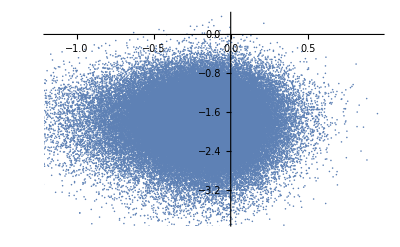
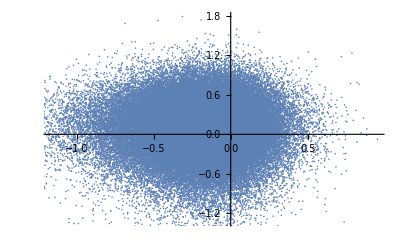

```mathematica
{ListPlot[{Z,Z1}ᵀ], ListPlot[{Z,Z2}ᵀ]}
```

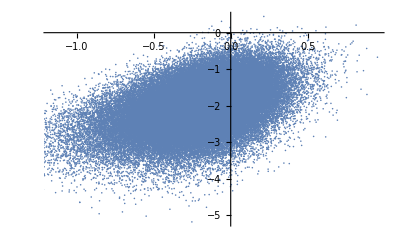
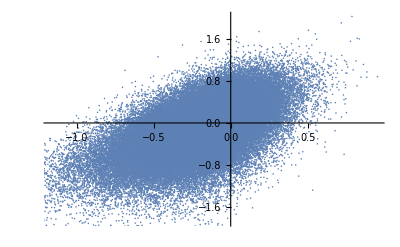

```mathematica
{ListPlot[{Z,X1}ᵀ],ListPlot[{Z,X2}ᵀ]}
```

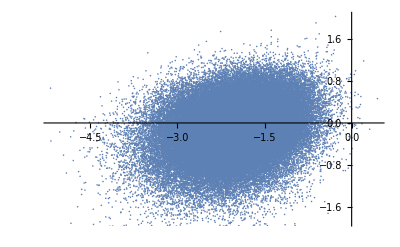

```mathematica
ListPlot[{X1, X2}ᵀ]
```

#### ML estimates of parameters

These work remarkably bad.

```mathematica
LL[α_,β_,μ_,δ_]:=Total[Log[g[X1[[1;;10]],α,β,μ,δ]]];NMaximize[{LL[α0,5,-1,3],α0>5}, α0]
```

{-96.3231,{α0→16.569}}

```mathematica
{LL[α,β,μ+μ1,δ+δ1],{α,β,μ+μ1,δ+δ1}}
```

{-10.0115,{8,-3,-1,2.5}}

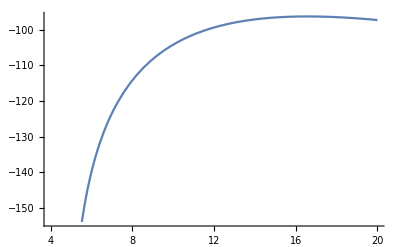

```mathematica
Plot[LL[α0, 5, -1, 3], {α0,4,20}]
```

```mathematica
LL[α_,β_,μ_,δ_]:=Total[Log[g[X1[[1;;10]],α,β,μ,δ]]];NMaximize[{LL[α0,β0,μ0,δ0],α0>2 && Abs[β0]<α0,δ0>0}, {α0,β0,μ0,δ0}]
{LL[α,β,μ+μ1,δ+δ1],{α,β,μ+μ1,δ+δ1}}
```

NMaximize::ivar: 0.00228454 is not a valid variable.

NMaximize[{log((α0 ⅇ^(δ0 √(α0^2-β0^2)-0.852964 β0) 1α0 √(1+0.727548/δ0^2) δ0)/(π √(0.727548/δ0^2+1)))+log((α0 ⅇ^(δ0 √(α0^2-β0^2)-1.03807 β0) 1α0 √(1+1.0776/δ0^2) δ0)/(π √(1.0776/δ0^2+1)))+log((α0 ⅇ^(δ0 √(α0^2-β0^2)-1.48448 β0) 1α0 √(1+2.20369/δ0^2) δ0)/(π √(2.20369/δ0^2+1)))+log((α0 ⅇ^(δ0 √(α0^2-β0^2)-1.51958 β0) 1α0 √(1+2.30912/δ0^2) δ0)/(π √(2.30912/δ0^2+1)))+log((α0 ⅇ^(δ0 √(α0^2-β0^2)-1.75867 β0) 1α0 √(1+3.0929/δ0^2) δ0)/(π √(3.0929/δ0^2+1)))+log((α0 ⅇ^(δ0 √(α0^2-β0^2)-1.87288 β0) 1α0 √(1+3.50767/δ0^2) δ0)/(π √(3.50767/δ0^2+1)))+log((α0 ⅇ^(δ0 √(α0^2-β0^2)-2.04234 β0) 1α0 √(1+4.17114/δ0^2) δ0)/(π √(4.17114/δ0^2+1)))+log((α0 ⅇ^(δ0 √(α0^2-β0^2)-2.378 β0) 1α0 √(1+5.65487/δ0^2) δ0)/(π √(5.65487/δ0^2+1)))+log((α0 ⅇ^(δ0 √(α0^2-β0^2)-2.70643 β0) 1α0 √(1+7.32476/δ0^2) δ0)/(π √(7.32476/δ0^2+1)))+log((α0 ⅇ^(δ0 √(α0^2-β0^2)-2.87083 β0) 1α0 √(1+8.24167/δ0^2) δ0)/(π √(8.24167/δ0^2+1))),α0>2∧Abs[β0]<α0,δ0>0},{α0,β0,0.00228454,δ0}]

{-10.0115,{8,-3,-1,2.5}}

```mathematica
LL[α_,β_,μ_,δ_]:=Total[Log[g[X2[[1;;10]],α,β,μ,δ]]];NMaximize[{LL[α0,β0,μ0,δ0],α0>2 && Abs[β0]<α0,δ0>0}, {α0,β0,μ0,δ0}]
{LL[α,β,μ+μ2,δ+δ2],{α,β,μ+μ2,δ+δ2}}
```

NMaximize::ivar: 0.00228454 is not a valid variable.

NMaximize[{log((α0 ⅇ^(δ0 √(α0^2-β0^2)-0.0184268 β0) 1α0 √(1+0.000339547/δ0^2) δ0)/(π √(0.000339547/δ0^2+1)))+log((α0 ⅇ^(δ0 √(α0^2-β0^2)+0.183634 β0) 1α0 √(1+0.0337213/δ0^2) δ0)/(π √(0.0337213/δ0^2+1)))+log((α0 ⅇ^(δ0 √(α0^2-β0^2)-0.240598 β0) 1α0 √(1+0.0578873/δ0^2) δ0)/(π √(0.0578873/δ0^2+1)))+log((α0 ⅇ^(δ0 √(α0^2-β0^2)-0.249281 β0) 1α0 √(1+0.0621413/δ0^2) δ0)/(π √(0.0621413/δ0^2+1)))+log((α0 ⅇ^(δ0 √(α0^2-β0^2)+0.290411 β0) 1α0 √(1+0.0843385/δ0^2) δ0)/(π √(0.0843385/δ0^2+1)))+log((α0 ⅇ^(δ0 √(α0^2-β0^2)-0.318356 β0) 1α0 √(1+0.101351/δ0^2) δ0)/(π √(0.101351/δ0^2+1)))+log((α0 ⅇ^(δ0 √(α0^2-β0^2)-0.383937 β0) 1α0 √(1+0.147407/δ0^2) δ0)/(π √(0.147407/δ0^2+1)))+log((α0 ⅇ^(δ0 √(α0^2-β0^2)+0.449226 β0) 1α0 √(1+0.201804/δ0^2) δ0)/(π √(0.201804/δ0^2+1)))+log((α0 ⅇ^(δ0 √(α0^2-β0^2)+0.504643 β0) 1α0 √(1+0.254665/δ0^2) δ0)/(π √(0.254665/δ0^2+1)))+log((α0 ⅇ^(δ0 √(α0^2-β0^2)-1.26287 β0) 1α0 √(1+1.59484/δ0^2) δ0)/(π √(1.59484/δ0^2+1))),α0>2∧Abs[β0]<α0,δ0>0},{α0,β0,0.00228454,δ0}]

{-6.69648,{8,-3,0.5,1.5}}

#### Method of moments

This performs much better

```mathematica
e1=Table[(Moment[X1,r]-D[M[u,α0,β0,μ10,δ10],{u,r}]/.u->0)==0, {r,1,4}];
sol1=NSolve[Flatten[{e1 ,δ10>0,α0>3, Abs[β0]<α0}], {α0,β0,μ10,δ10}]
{α,β,μ+μ1, δ+δ1}
```

{{α0→8.88521,μ10→-0.863562,δ10→2.71492,β0→-3.45756}}

{8,-3,-1,2.5}

```mathematica
e2=Table[(Moment[X2,r]-D[M[u,α0,β0,μ20,δ20],{u,r}]/.u->0)==0, {r,1,4}];
sol2=NSolve[Flatten[{e2 ,δ20>0,α0>3, Abs[β0]<α0}], {α0,β0,μ20,δ20}]
{α,β,μ+μ2, δ+δ2}
```

{{α0→8.27586,μ20→0.527967,δ20→1.55051,β0→-3.13777}}

{8,-3,0.5,1.5}

```mathematica
e1=Table[(Moment[X1,r]-D[M[u,α0,β0,μ10,δ10],{u,r}]/.u->0), {r,1,4}];
e2=Table[(Moment[X2,r]-D[M[u,α0,β0,μ20,δ20],{u,r}]/.u->0), {r,1,4}];
```

```mathematica
e=RootMeanSquare[Flatten[Join[e1,e2]]];
cons={δ10>0,δ20>0,α0>Min[α0/.sol1⟦1⟧,α0/.sol2⟦1⟧],α0<Max[α0/.sol1⟦1⟧,α0/.sol2⟦1⟧],Abs[β0]<α0};
sol=NMinimize[{e,cons},{α0,β0,μ10,δ10,μ20,δ20}]
```

NMinimize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{0.00215967,{α0→8.39416,β0→-2.76949,μ10→-1.03141,δ10→2.79654,μ20→0.481272,δ20→1.69088}}

```mathematica
{α,β,μ1, δ1, μ2, δ2}
```

{8,-3,-1,2,0.5,1}

```mathematica
sol3=NSolve[Correlation[X1,X2]==δ0/(√((δ0+δ10/.sol⟦2⟧) (δ0+δ20/.sol⟦2⟧))),δ0]
```

{{δ0→0.767044}}

```mathematica
{Correlation[X1,X2],δ0/(√((δ0+δ10/.sol⟦2⟧) (δ0+δ20/.sol⟦2⟧)))/.sol3⟦1⟧,δ/(√((δ+δ1) (δ+δ2)))}
```

{0.259175,0.259175,0.258199}

WLOG set μ to zero.

### Modules

```mathematica
FitNIG[data_]:=Module[{e,α,β,μ,δ,sol1},
e=Table[(Moment[data,r]-D[M[u,α,β,μ,δ],{u,r}]/.u->0)==0, {r,1,4}];
sol1=NSolve[Flatten[{e ,δ>0,α>3, Abs[β]<α}], {α,β,μ,δ}];
{α,β,μ,δ}/.sol1[[1]]
]
```

```mathematica
FitJointNIG[d1_,d2_,αlb_,αub_]:=Module[{e1,e2,α,β,μ1,μ2,δ1,δ2,e,cons,sol},
e1=Table[(Moment[d1,r]-D[M[u,α,β,μ1,δ1],{u,r}]/.u->0), {r,1,4}];
e2=Table[(Moment[d2,r]-D[M[u,α,β,μ2,δ2],{u,r}]/.u->0), {r,1,4}];
e=RootMeanSquare[Flatten[Join[e1,e2]]];cons={δ1>0,δ2>0,αlb<α<αub,Abs[β]<α};sol=NMinimize[{e,cons},{α,β,μ1,δ1,μ2,δ2}];
{α,β,μ1,δ1,μ2,δ2}/.sol⟦2⟧
]
```

```mathematica
FitCorrelation[data1_,data2_,δ1_,δ2_]:=Module[{δ,sol3},
sol3=NSolve[Correlation[data1,data2]==δ/(√((δ1) (δ2))),δ];
δ/.sol3⟦1⟧
]
```

### Read BTC data

```mathematica
data=Import[NotebookDirectory[]<> "../processed_data/btc_future_crix.csv"];
```

```mathematica
Dimensions[data]
```

{646,14}

```mathematica
data[[1;;10,12;;13]]
```

(return_btc | return_brr
-0.0226425 | -0.0564519
-0.0667516 | -0.0409618
-0.0522745 | -0.0463652
0.020076 | 0.0120735
0.0174733 | 0.0233977
0.0252517 | 0.0109912
-0.0252517 | -0.012727
0.016472 | 0.00609231
-0.0427781 | -0.0313833)

```mathematica
rbtc=data[[2;;,12]];
rbrr=data[[2;;,13]];
```

```mathematica
Correlation[rbrr,rbtc]
```

0.788286

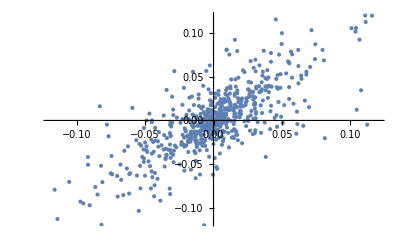

```mathematica
ListPlot[{rbrr,rbtc}ᵀ]
```

```mathematica
{α1,β1,μ1,δ1}=FitNIG[rbrr]
```

{20.1791,-1.11329,0.00228454,0.0350148}

```mathematica
{α2,β2,μ2,δ2}=FitNIG[rbtc]
```

{16.4365,-1.04596,0.00258213,0.0349328}

```mathematica
{α,β,μ1, δ1, μ2, δ2}=FitJointNIG[rbrr,rbtc,Min[α1,α2],Max[α1,α2]]
```

{17.6612,-1.06607,0.00220125,0.030616,0.00262596,0.0375604}

```mathematica
δ=FitCorrelation[rbrr,rbtc,δ1, δ2]
```

0.0267315

Make delta’s incremental

```mathematica
δ1=δ1-δ;
δ2=δ2-δ;
```

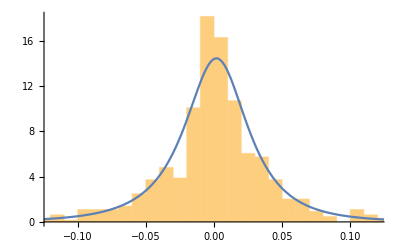
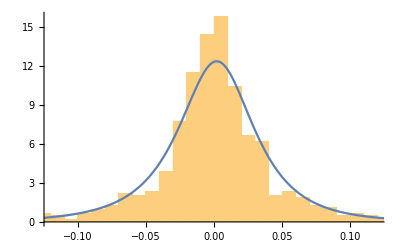

```mathematica
{Show[
Histogram[rbrr, Automatic, "PDF"],
Plot[g[x,α,β,μ1,δ+δ1], {x,-0.3,0.3},PlotRange->All]
],
Show[Histogram[rbtc, Automatic, "PDF"],
Plot[g[x,α,β,μ2,δ+δ2], {x,-0.3, 0.3}, PlotRange->All]
]
}
```

#### Hedge

Z + Z_1-h (Z+Z_2)=(1-h)Z + Z_1-h Z_2

```mathematica
{δ, δ1, δ2}
```

{0.0267315,0.00388452,0.0108289}

```mathematica
γ=√(α^2-β^2);
h=0.95;
x=0.01;
Timing[NIntegrate[CDF[NormalDistribution[μ1-h μ2+β z1-h β z2, √((1-h)^2 z+z1+h^2 z2)], x]PDF[InverseGaussianDistribution[δ/γ, δ^2], z]PDF[InverseGaussianDistribution[δ1/γ,δ1^2], z1] 
PDF[InverseGaussianDistribution[δ2/γ,δ2^2], z2], {z,0,∞},{z1,0,∞}, {z2,0,∞}]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{5.24155,0.733644}

Approximate distribution of hedged position by NIG (it’s not exactly NIG because of the scaling with h, but close as h is close to 1). Match moments.

```mathematica
g1 = M[u,αh, βh, μh, δh]
```

ⅇ^(δh (√(αh^2-βh^2)-√(αh^2-(βh+u)^2))+μh u)

```mathematica
g2=M[u,α/(1-h),β/(1-h),0,δ (1-h)] M[u,α,β,μ1,δ1] M[-u,α/h,β/h,h μ2,h δ2]
```

exp(0.0102875 (18.5569-√(345.616-(-u-1.12217)^2))+0.00133657 (352.58-√(124767.-(u-21.3213)^2))+0.00388452 (17.629-√(311.918-(u-1.06607)^2))-0.000293415 u)

```mathematica
{D[g2, {u,1}]/.{u->0},ENIG[αh,βh,μh,δh]/.sol⟦1⟧}
```

ReplaceAll::reps: {0.00215967} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

{0.0000129598,(βh δh)/(√(αh^2-βh^2))+μh/.0.00215967}

```mathematica
{D[g2, {u,2}]/.{u->0},VNIG[αh,βh,μh,δh]+ENIG[αh,βh,μh,δh]^2/.sol⟦1⟧,VNIG[αh,βh,-(βh δh)/(√(αh^2-βh^2)),δh]/.sol⟦1⟧}
```

ReplaceAll::reps: {0.00215967} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

{0.000781361,((βh δh)/(√(αh^2-βh^2))+μh)^2+(αh^2 δh)/((αh^2-βh^2)^(3/2))/.0.00215967,(αh^2 δh)/((αh^2-βh^2)^(3/2))/.0.00215967}

```mathematica
sol=NSolve[Flatten[Join[Table[D[g1,{u,r}]==D[g2,{u,r}]/.{u->0}, {r,1,4}],{αh>0,δh>0}]],{αh,βh,μh,δh}]
```

{{αh→18.1902,μh→-0.000335343,δh→0.0142003,βh→0.446033}}

```mathematica
{α,β,μ1+(1-h)μ2,δ}
```

{17.6612,-1.06607,0.00233255,0.0267315}

```mathematica
Dynamic[x]
```

```mathematica
Timing[t1=Table[NIntegrate[g[y,αh,βh,μh,δh]/.sol[[1]], {y,-∞,x}], {x,-0.1, 0.1,0.01}]]
```

{0.273819,{0.00570724,0.00782885,0.0108827,0.0153775,0.0221833,0.032874,0.0505134,0.0816378,0.141708,0.268281,0.50514,0.736644,0.85853,0.917107,0.947935,0.965656,0.976534,0.983541,0.98822,0.991433,0.993688}}

```mathematica
γ=√(α^2-β^2);
Timing[t2=Table[NIntegrate[CDF[NormalDistribution[μ1-h μ2+β z1-h β z2, √((1-h)^2 z+z1+h^2 z2)], x]PDF[InverseGaussianDistribution[δ/γ, δ^2], z]PDF[InverseGaussianDistribution[δ1/γ,δ1^2], z1] 
PDF[InverseGaussianDistribution[δ2/γ,δ2^2], z2], {z,0,∞},{z1,0,∞}, {z2,0,∞}],{x,-0.1, 0.1,0.01}]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{95.5086,{0.0056415,0.00773917,0.0107617,0.0152164,0.0219725,0.0326076,0.0502028,0.0813597,0.14174,0.268883,0.503343,0.733644,0.857141,0.916548,0.947699,0.965554,0.97649,0.983525,0.988217,0.991435,0.993693}}

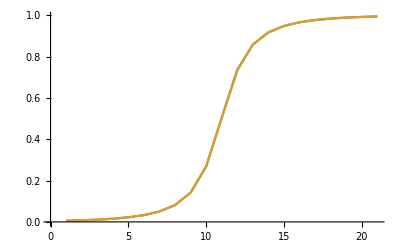

```mathematica
ListPlot[{t1,t2},Joined->True]
```